## Homogen System

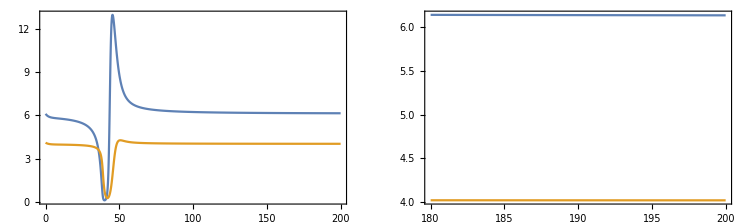

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x[1,1][t]→0. | x[2,1][t]→-5.
x[1,1][t]→0. | x[2,1][t]→0.
x[1,1][t]→1.54205 | x[2,1][t]→1.98165
x[1,1][t]→6. | x[2,1][t]→4.
x[1,1][t]→6.12462 | x[2,1][t]→4.01835
x[1,1][t]→15. | x[2,1][t]→0.

```mathematica
Kx=15;
X0=6.1;Y0=4.1;

Tmax=200; 
EvaluateHomogenSystem[Tmax];
solHomogen=solveHomogen[Tmax];

GraphicsGrid[{
{Plot[solHomogen,{t,0,Tmax},PlotRange->Full,Frame->True],
Plot[solHomogen,{t,Tmax*0.9,Tmax},PlotRange->Full,Frame->True]}
}]

SteadyStates=Solve[{rhs[1,1]==0,rhs[2,1]==0},{x[1,1][t],x[2,1][t]}]//FullSimplify;
TableForm[SteadyStates]
```

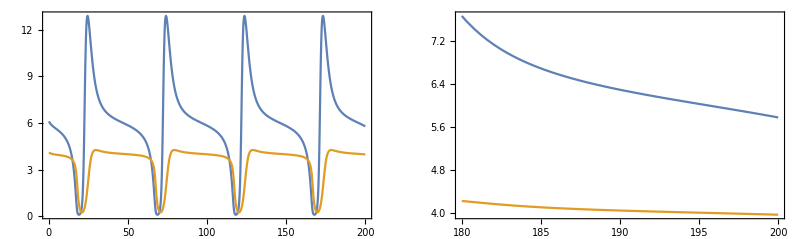

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x[1,1][t]→0. | x[2,1][t]→-5.
x[1,1][t]→0. | x[2,1][t]→0.
x[1,1][t]→1.53959 | x[2,1][t]→1.97829
x[1,1][t]→6.01354-0.631177 ⅈ | x[2,1][t]→4.01086-0.0934588 ⅈ
x[1,1][t]→6.01354+0.631177 ⅈ | x[2,1][t]→4.01086+0.0934588 ⅈ
x[1,1][t]→14.9 | x[2,1][t]→0.

```mathematica
Kx=14.9;
X0=6.1;Y0=4.1;

Tmax=200;
EvaluateHomogenSystem[Tmax];
solHomogen=solveHomogen[Tmax];

GraphicsGrid[{
{Plot[solHomogen,{t,0,Tmax},PlotRange->Full,Frame->True],
Plot[solHomogen,{t,Tmax*0.9,Tmax},PlotRange->Full,Frame->True]}
}]

SteadyStates=Solve[{rhs[1,1]==0,rhs[2,1]==0},{x[1,1][t],x[2,1][t]}]//FullSimplify;
TableForm[SteadyStates]
```

## Solver Test

```mathematica
PlotOptionsTimeSeries={PlotRange->Full,ImageSize->Small,MaxPlotPoints->1000};
```

### Local

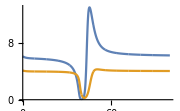

```mathematica
Kx=15;
X0=6.1;Y0=4.1;
EulerLocal[];
pltLocal=ListLinePlot[Transpose[data],ImageSize->Small,DataRange->{0,Tmax},PlotRange->Full]
```

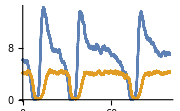

```mathematica
Kx=15;
X0=6.1;Y0=4.1;
EulerMaruyamaLocal[0.1]
pltLocalNoise=ListLinePlot[Transpose[data],ImageSize->Small,DataRange->{0,Tmax},PlotRange->Full]
```

### Spatial

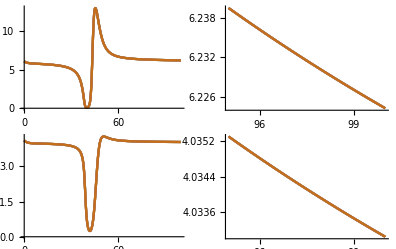

```mathematica
Kx=15;
X0=6.1;Y0=4.1;
maxsteps=10000;
Tmax=100;
EulerSpatial[Tmax,maxsteps];
pltSpatial=GraphicsGrid[{{
ListLinePlot[Transpose[data[[All,1]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,1]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]},
{ListLinePlot[Transpose[data[[All,2]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,2]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]
}}]
```

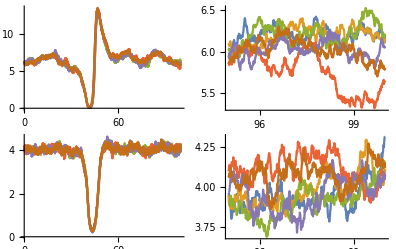

```mathematica
Kx=15;
X0=6.1;Y0=4.1;
maxsteps=10000;
Tmax=100;
EulerMaruyamaSpatial[0.1,Tmax,maxsteps];
pltSpatialNoise=GraphicsGrid[{{
ListLinePlot[Transpose[data[[All,1]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,1]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]},
{ListLinePlot[Transpose[data[[All,2]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,2]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]
}}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

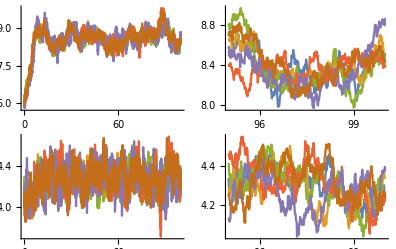

```mathematica
Kx=16;
X0=6.1;Y0=4.1;
maxsteps=10000;
Tmax=100;
EulerMaruyamaSpatialFixedRoot[0.1,Tmax,maxsteps];
pltSpatialNoise=GraphicsGrid[{{
ListLinePlot[Transpose[data[[All,1]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,1]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]},
{ListLinePlot[Transpose[data[[All,2]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,2]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]
}}]
```

```mathematica
data[[1000,All,All]]
```

{{3.37908,3.20738,3.33246,3.14819,3.3361,3.41615},{3.65762,3.73671,3.76762,3.38858,3.79458,3.5792}}

### Local variable Kx

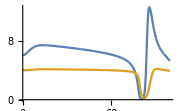

```mathematica
X0=6.1;Y0=4.1;
EulerLocalVariable[{15.5,14.5}];
pltLocal=ListLinePlot[Transpose[data],ImageSize->Small,DataRange->{0,Tmax},PlotRange->Full]
```

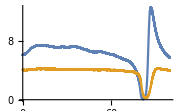

```mathematica
X0=6.1;Y0=4.1;
EulerMaruyamaLocalVariable[{15.5,14.5},0.01]
pltLocalNoise=ListLinePlot[Transpose[data],ImageSize->Small,DataRange->{0,Tmax},PlotRange->Full]
```

### Spatial variable Kx

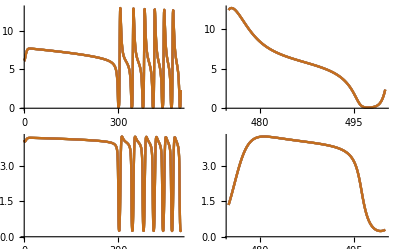

```mathematica
EulerSpatialVariable[{15.5,14.5}];
pltSpatial=GraphicsGrid[{{
ListLinePlot[Transpose[data[[All,1]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,1]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]},
{ListLinePlot[Transpose[data[[All,2]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,2]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]
}}]
```

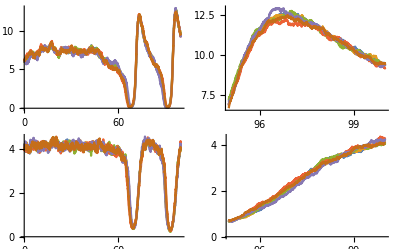

```mathematica
EulerMaruyamaSpatialVariable[{15.5,14.5},0.1];
pltSpatial=GraphicsGrid[{{
ListLinePlot[Transpose[data[[All,1]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,1]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]},
{ListLinePlot[Transpose[data[[All,2]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,2]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]
}}]
```

## Data Set Stable

### header

```mathematica
SetDirectory["/imports/junko.work/brechtel/Early Warning Signs/Saddle Node/export"];
```

```mathematica
ExportData2S6P[name_,data_]:=Module[{},
Export[name<>".CSV",Table[Join[data[[i,1]],data[[i,2]]],{i,maxsteps}]]
];
```

```mathematica
GenFileName[]:="2_Species_6_Patches_"<>StringReplace["Kx="<>ToString[Kx]<>"_noise="<>ToString[noise],"."->"_"];
```

```mathematica
ParameterTrajectory[pars0_,pars1_,a_]:=pars0+a(pars1-pars0);
```

```mathematica
PlotOptionsTimeSeries={PlotRange->Full,ImageSize->Small,MaxPlotPoints->1000};
```

### constant pars

```mathematica
parameterList=Table[ParameterTrajectory[15.1,14.9,a],{a,0,1,0.25}]
Length[parameterList]
assf=0
```

{15.1,15.05,15.,14.95,14.9}

5

0

1

15.1

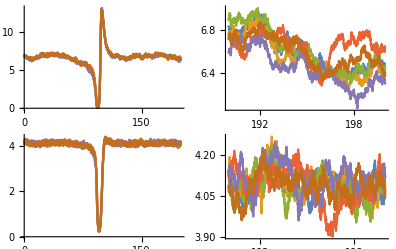

1

2_Species_6_Patches_Kx=15_1_noise=0_05

```mathematica
++assf
Kx=parameterList[[assf]]
noise=0.05;

(* Transienten *)
Tmax0=100;
maxsteps0=100000;
EulerMaruyamaSpatial[noise,Tmax0,maxsteps0];

initialData=data[[maxsteps0]];

(* Daten nach Einschwingen *)
Tmax=200;
maxsteps=200000;
EulerMaruyamaSpatial[noise,Tmax,maxsteps,initialData];
pltSpatialNoise=GraphicsGrid[{{
ListLinePlot[Transpose[data[[All,1]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,1]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]},
{ListLinePlot[Transpose[data[[All,2]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,2]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]
}}]

assf
GenFileName[]
```

```mathematica
parameterList=Table[Kx,{Kx,14.99,15.01,0.001}];
parameterList//Length
```

21

```mathematica
parameterList=Table[Kx,{Kx,14.99,15.01,0.001}];
For[assf=1,assf<=Length[parameterList],++assf,
Kx=parameterList[[assf]];
noise=0.01;

(* Transienten *)
Tmax0=100;
maxsteps0=100000;
EulerMaruyamaSpatial[noise,Tmax0,maxsteps0];

initialData=data[[maxsteps0]];

(* Daten nach Einschwingen *)
Tmax=200;
maxsteps=200000;
EulerMaruyamaSpatial[noise,Tmax,maxsteps,initialData];

ExportData2S6P[GenFileName[],data];
];
```

### variable phi

```mathematica
GenFileName[]:="2_Species_6_Patches_"<>StringReplace["Kx="<>ToString[KxInterval[[1]]]<>"_to_"<>ToString[KxInterval[[2]]]<>"_noise="<>ToString[noise],"."->"_"];
GenFileName[tag_]:="2_Species_6_Patches_"<>StringReplace["Kx="<>ToString[KxInterval[[1]]]<>"_to_"<>ToString[KxInterval[[2]]]<>"_noise="<>ToString[noise],"."->"_"]<>"_("<>ToString[tag]<>")";
```

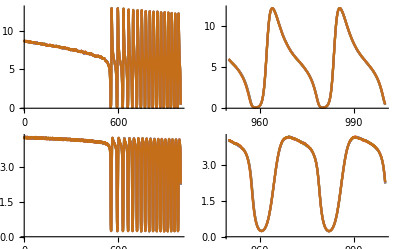

2_Species_6_Patches_Kx=16_to_14_noise=0_01

```mathematica
(* Parameter *)
KxInterval={15.1,14.9};
noise=0.01;

(* Transienten *)
Tmax0=100;
maxsteps0=100000;

Kx=KxInterval[[1]];
EulerMaruyamaSpatial[noise,Tmax0,maxsteps0];
initialData=data[[maxsteps0]];

(* Daten nach Einschwingen *)
Tmax=1000;
maxsteps=1000000;
EulerMaruyamaSpatialVariable[KxInterval,noise,Tmax,maxsteps,initialData];
pltSpatialNoise=GraphicsGrid[{{
ListLinePlot[Transpose[data[[All,1]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,1]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]},
{ListLinePlot[Transpose[data[[All,2]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,2]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]
}}]
GenFileName[]
```

```mathematica
SetDirectory["/imports/junko.work/brechtel/Early Warning Signs/Time Series/Continuous changing parameters"]

(* Parameter *)
KxInterval={15.1,14.9};
noise=0.01;

(* Transienten *)
Tmax0=100;
maxsteps0=100000;

Kx=KxInterval[[1]];

EulerMaruyamaSpatial[noise,Tmax0,maxsteps0];
initialData=data[[maxsteps0]];

(* Daten nach Einschwingen *)
Tmax=4200;
maxsteps=4200000;
EulerMaruyamaSpatialVariable[KxInterval,noise,Tmax,maxsteps,initialData];

ExportData2S6P[GenFileName[],data];
```

SetDirectory::cdir: Cannot set current directory to /local.work/brechtel/Early Warning Signs/Time Series/Continuous changing parameters.

$Failed

## Fixed Root

### header

```mathematica
SetDirectory["/imports/junko.work/brechtel/Early Warning Signs/Saddle Node/export/Fixed Root"];
```

```mathematica
ExportData2S6P[name_,data_]:=Module[{},
Export[name<>".CSV",Table[Join[data[[i,1]],data[[i,2]]],{i,maxsteps}]]
];
```

```mathematica
GenFileName[]:="2_Species_6_Patches_"<>StringReplace["Kx="<>ToString[Kx]<>"_noise="<>ToString[noise],"."->"_"];
```

```mathematica
ParameterTrajectory[pars0_,pars1_,a_]:=pars0+a(pars1-pars0);
```

```mathematica
PlotOptionsTimeSeries={PlotRange->Full,ImageSize->Small,MaxPlotPoints->1000};
```

### constant parameter

```mathematica
parameterList=Table[ParameterTrajectory[15.1,14.9,a],{a,0,1,0.25}]
Length[parameterList]
assf=0
```

{15.1,15.05,15.,14.95,14.9}

5

0

5

14.9

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

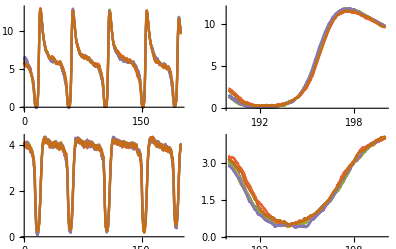

5

2_Species_6_Patches_Kx=14_9_noise=0_05

```mathematica
++assf
Kx=parameterList[[assf]]
noise=0.05;

(* Transienten *)
Tmax0=100;
maxsteps0=100000;
EulerMaruyamaSpatialFixedRoot[noise,Tmax0,maxsteps0];

initialData=data[[maxsteps0]];

(* Daten nach Einschwingen *)
Tmax=200;
maxsteps=200000;
EulerMaruyamaSpatialFixedRoot[noise,Tmax,maxsteps,initialData];
pltSpatialNoise=GraphicsGrid[{{
ListLinePlot[Transpose[data[[All,1]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,1]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]},
{ListLinePlot[Transpose[data[[All,2]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,2]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]
}}]

assf
GenFileName[]
```

```mathematica
parameterList=Table[Kx,{Kx,14.9,15.1,0.01}];
For[assf=1,assf<=Length[parameterList],++assf,
Kx=parameterList[[assf]];
noise=0.01;

(* Transienten *)
Tmax0=100;
maxsteps0=100000;
EulerMaruyamaSpatialFixedRoot[noise,Tmax0,maxsteps0];

initialData=data[[maxsteps0]];

(* Daten nach Einschwingen *)
Tmax=200;
maxsteps=200000;
EulerMaruyamaSpatialFixedRoot[noise,Tmax,maxsteps,initialData];

ExportData2S6P[GenFileName[],data];
];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.